数学实验第三次作业

何雨蓬 3018233063

1.求下列级数的和

```mathematica
Sum[1/(n^2),{n,1,Infinity}]
```

π^2/6

```mathematica
Sum[1/(n*Log[n]),{n,1,Infinity}]
```

Power::infy: 碰到无穷表达式 1/0.

∑_(n=1)^∞ 1/(n Log[n])

```mathematica
Sum[(2n-1)/(2^n) *x^(2(n-1)),{n,1,Infinity}]
```

(2+x^2)/((-2+x^2)^2)

```mathematica
Sum[n*(x-1)^n,{n,1,Infinity}]
```

(-1+x)/(-2+x)^2

2.求下列函数展开成x0点的幂级数

```mathematica
Series[(1+x)/(1-x)^3,{x,0,6}]
```

1+4 x+9 x^2+16 x^3+25 x^4+36 x^5+49 x^6+O[x]^7

```mathematica
Series[ArcTan[(1+x)/(1-x)],{x,0,5}]
```

π/4+x-x^3/3+x^5/5+O[x]^6

```mathematica
Series[Log[1/(1+2x+x^2)],{x,-1,8}]
```

Log[1/(1+x)^2]+O[x+1]^9

3.将函数f(x)展开成Fourier级数

(-2-ⅈ) ⅇ^(-ⅈ x)-(2-ⅈ) ⅇ^(ⅈ x)+(1/2+ⅈ/2) ⅇ^(-2 ⅈ x)+(1/2-ⅈ/2) ⅇ^(2 ⅈ x)-(2/9+ⅈ/3) ⅇ^(-3 ⅈ x)-(2/9-ⅈ/3) ⅇ^(3 ⅈ x)+(1/8+ⅈ/4) ⅇ^(-4 ⅈ x)+(1/8-ⅈ/4) ⅇ^(4 ⅈ x)-(2/25+ⅈ/5) ⅇ^(-5 ⅈ x)-(2/25-ⅈ/5) ⅇ^(5 ⅈ x)+(1/18+ⅈ/6) ⅇ^(-6 ⅈ x)+(1/18-ⅈ/6) ⅇ^(6 ⅈ x)-(2/49+ⅈ/7) ⅇ^(-7 ⅈ x)-(2/49-ⅈ/7) ⅇ^(7 ⅈ x)+(1/32+ⅈ/8) ⅇ^(-8 ⅈ x)+(1/32-ⅈ/8) ⅇ^(8 ⅈ x)-(2/81+ⅈ/9) ⅇ^(-9 ⅈ x)-(2/81-ⅈ/9) ⅇ^(9 ⅈ x)+(1/50+ⅈ/10) ⅇ^(-10 ⅈ x)+(1/50-ⅈ/10) ⅇ^(10 ⅈ x)+π^2/3

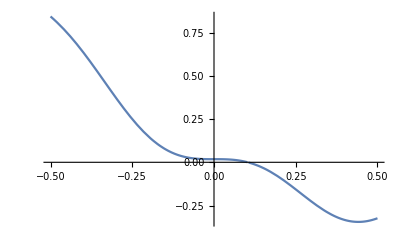

```mathematica
FourierSeries[x^2-x,x,10]
Plot[%,{x,-1/2,1/2}]
```

4.将函数f(x)展开成正弦级数

Sin[x]+1/2 Sin[2 x]+1/3 Sin[3 x]+1/4 Sin[4 x]+1/5 Sin[5 x]+1/6 Sin[6 x]+1/7 Sin[7 x]+1/8 Sin[8 x]+1/9 Sin[9 x]+1/10 Sin[10 x]

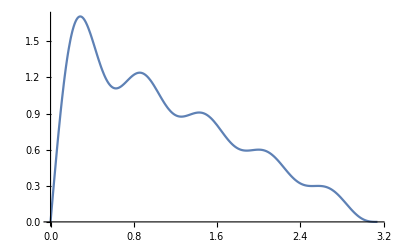

```mathematica
FourierSinSeries[(Pi-x)/2,x,10]
Plot[%,{x,0,Pi}]
```

5.求下列一阶微分方程的通解

```mathematica
DSolve[y'[x]*Tan[x]-y[x]==α,y[x],x]
```

{{y[x]→-α+C[1] Sin[x]}}

```mathematica
DSolve[3ⅇ^x *Tan[y[x]]+(1-ⅇ^x)Sec[y[x]]^2 *y'[x]==0,y[x],x]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{y[x]→ArcCot[ⅇ^(-2 C[1])/((-1+ⅇ^x)^3)]}}

6.求下列一阶微分方程满足初始条件的特解

```mathematica
DSolve[{y'[x]*Sin[x]==y[x]*Log[y[x]],y[Pi/2]==ⅇ},y[x],x]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{y[x]→ⅇ^Tan[x/2]}}

```mathematica
DSolve[{y'[x]==y[x]/x+Tan[y[x]/x],y[1]==Pi/6},y[x],x]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{y[x]→x ArcSin[x/2]}}

7.求下列高阶微分方程的通解

```mathematica
DSolve[y''[x]==x+ⅇ^x,y[x],x]
```

{{y[x]→ⅇ^x+x^3/6+C[1]+x C[2]}}

```mathematica
DSolve[y[x]*y''[x]+y'[x]^2==0,y[x],x]
```

{{y[x]→√(2 x-C[1]) C[2]}}

8.求下列微分方程初值问题的解

```mathematica
DSolve[{y''[x]+Pi^2*y[x]==0,y[0]==1,y'[0]==Pi},y[x],x]
```

{{y[x]→Cos[π x]+Sin[π x]}}

```mathematica
DSolve[{y''[x]-y[x]==4x*ⅇ^x,y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→ⅇ^-x (-1+ⅇ^(2 x)-ⅇ^(2 x) x+ⅇ^(2 x) x^2)}}

9.求初值问题在点x=0.5处的数值解，并作出图形

```mathematica
a=NDSolve[{y'[x]==x^2+y[x]^2,y[0]==1},y[x],{x,0,0.9}]
```

{{y[x]→InterpolatingFunction[{{0., 0.9}}, <>][x]}}

```mathematica
Solution=a[[1,1,2,0]]
```

InterpolatingFunction[{{0., 0.9}}, <>]

```mathematica
Solution[0.5]
```

2.067

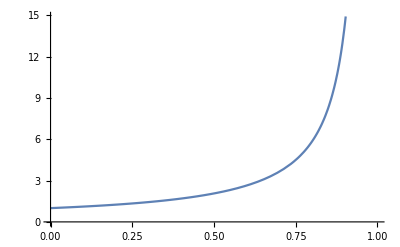

```mathematica
Plot[Solution[x],{x,0,1}]
```